```mathematica
SetOptions[LogLogPlot, BaseStyle -> {FontFamily -> "Gill Sans", FontSize -> 14},Frame->True];
```

```mathematica
Defining Variables
```

```mathematica
b = 6.3; (*kpc*)
Rmax =65*b;(*kpc*)
mlow = 10^5;(*M_sun*)
mhigh = 10^8; (*M_sun*)
sigmac = 3*10^9;(*M_sun/kpc^2*) 
A = 1/(π b^2);
a0=2.0577*10^-6;
dNdm[m_] := a0(m/(2.52*10^7))^-1.9;
rs0 = 1; (*kpc*)
γ=1/3;
rsm[m_]:= rs0(m/10^9)^γ;(*kpc*)
f = 0.2;
Ps[rs_,m_]:= 1/(√(2 π)f rsm[m])Exp[-1/2((rs - rsm[m])/(f rsm[m]))^2];
ν=2/3;(*isothermal*)
(*ν=1;(*NFW*)*)
r3d0 = 100;(*kpc*)
rt0 = 1;(*kpc*)
rtm[m_,r3d_]:=(m/10^6)^(1/3)(r3d/100)^ν;(*kpc*)
Pt[rt_,m_]:=1/(ν Rmax)r3d0/rt((10^6/m)^(1/3)rt/rt0)^(1/ν);
```

```mathematica
tau[m_,r3d_]:=rtm[m,r3d]/rsm[m];
```

```mathematica
For P_s,P_t = delta func
```

```mathematica
τ = 15;
n = (τ^2/((τ^2+1)^2))((τ^2-1) Log[τ] + τ π-(τ^2+1)); 
x[r_,m_] := r/rsm[m]; 
F[r_,m_]:=ArcCos[1/x[r,m]]/(√(x[r,m]^2-1)); 
L[r_,m_]:=Log[x[r,m]/(√(τ^2+x[r,m]^2)+τ)];
kappa[r_,m_]:=1/sigmac(m/(n*rsm[m]^2))(τ^2/(2π(τ^2+1)^2))(((τ^2+1)/(x[r,m]^2-1))(1-F[r,m])+2F[r,m]-(π/(√(τ^2+x[r,m]^2)))+((τ^2-1)/(τ √(τ^2+x[r,m]^2)))L[r,m]);
```

```mathematica
κ[k_,m_] :=NIntegrate[r BesselJ[0,k r] kappa[r,m],{r,0,2*Rmax},Method->"LevinRule",MaxRecursion->14];
mytableps3 = Flatten[ParallelTable[{10^i,10^j,κ[10^i,10^j]^2*dNdm[10^j]},{i,-2,3,0.1},{j,Log10[mlow],Log10[mhigh],0.1}],1];
approxfunc3 = Interpolation[mytableps3];
```

```mathematica
Pk=ParallelTable[{10^i,NIntegrate[A*4*π^2 approxfunc3[10^i,m],{m,mlow,mhigh}]},{i,-2,3,0.1}];
```

Point masses

```mathematica
Pkptmass=A/sigmac^2*Integrate[dNdm[m]*m^2,{m,mlow,mhigh}];
ptmasstable = ParallelTable[{10^i,Pkptmass},{i,-2,3,0.1}];
```

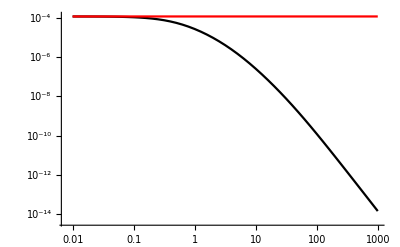

```mathematica
ListLogLogPlot[{Pk,ptmasstable},Joined->True,PlotStyle->{Black,Red}]
```

```mathematica
P_s = normal dist, P_t = delta func
```

```mathematica
xs[r_,rs_] := r/rs; 
Fs[r_,rs_]:=ArcCos[1/xs[r,rs]]/(√(xs[r,rs]^2-1)); 
Ls[r_,rs_]:=Log[xs[r,rs]/(√(τ^2+xs[r,rs]^2)+τ)];
kappas[r_,rs_] :=1/sigmac(1/(n rs^2))(τ^2/(2 π (τ^2+1)^2))(((τ^2+1)/(xs[r,rs]^2-1))(1-Fs[r,rs])+2Fs[r,rs]-(π/(√(τ^2+xs[r,rs]^2)))+((τ^2-1)/(τ √(τ^2+xs[r,rs]^2))) Ls[r,rs]);
κs[k_,rs_] :=NIntegrate[r BesselJ[0,k r] kappas[r,rs],{r,0,2Rmax},Method->"LevinRule",MaxRecursion->14];
```

```mathematica
TablePs = Flatten[ParallelTable[{10^i,10^j,10^s,κs[10^i,10^s]^2 Ps[10^s,10^j]},{i,-2,3,0.2},{j,Log10[mlow],Log10[mhigh],0.1},{s,Log10[0.00001],Log10[7],0.15}],2];
FuncPs=Interpolation[TablePs];
```

```mathematica
rsmax = N[rsm[mhigh]];
```

```mathematica
Ints = Flatten[ParallelTable[{10^i,10^j,NIntegrate[FuncPs[10^i,10^j,rs],{rs,0,9*rsmax}]},{i,-2,3,0.2},{j,Log10[mlow],Log10[mhigh],0.1}],1];
FuncPs2 = Interpolation[Ints];
```

```mathematica
Pks=ParallelTable[{10^i,NIntegrate[A* 4* π^2* FuncPs2[10^i,m] dNdm[m] m^2,{m,mlow,mhigh}]},{i,-2,3,0.2}];
```

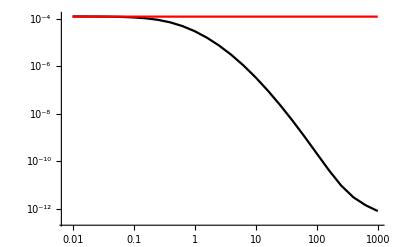

```mathematica
ListLogLogPlot[{Pks,ptmasstable},Joined->True,PlotStyle->{Black,Red}]
```

```mathematica
P_s = delta func, P_t = dist
```

```mathematica
xt[r_,rt_] := (τ r)/rt;
Ft[r_,rt_]:=ArcCos[1/xt[r,rt]]/(√(xt[r,rt]^2-1)); 
Lt[r_,rt_]:=Log[xt[r,rt]/(√(τ^2+xt[r,rt]^2)+τ)];
Smd[r_,rt_]:=(τ^2/(n rt^2))(τ^2/(2 π (τ^2+1)^2))(((τ^2+1)/(xt[r,rt]^2-1))(1-Ft[r,rt])+2Ft[r,rt]-(π/(√(τ^2+xt[r,rt]^2)))+((τ^2-1)/(τ √(τ^2+xt[r,rt]^2)))*Lt[r,rt]);
kappat[r_,rt_] :=Smd[r,rt]/sigmac;
```

```mathematica
kappat2[k_,rt_] :=NIntegrate[r BesselJ[0,k r] kappat[r,rt],{r,0,2*Rmax},Method->"LevinRule",MaxRecursion->14]; 
MyTablePt = Flatten[ParallelTable[{10^i,10^j,10^t,Re[kappat2[10^i,10^t]^2 Pt[10^t,10^j]]},{i,-2,3,0.2},{j,Log10[mlow],Log10[mhigh],0.1},{t,0,Log10[rtm[mhigh,Rmax]],0.15}],2];
MyApproxfunc2 = Interpolation[MyTablePt];
```

```mathematica
Int = Flatten[ParallelTable[{10^i,10^j,NIntegrate[MyApproxfunc2[10^i,10^j,rt],{rt,0,rtm[10^j,Rmax]}]},{i,-2,3,0.2},{j,Log10[mlow],Log10[mhigh],0.1}],1];
MyApproxfunc3 = Interpolation[Int];
```

```mathematica
Pkt=ParallelTable[{10^i,NIntegrate[A*4*π^2 MyApproxfunc3[10^i,m] dNdm[m] m^2,{m,mlow,mhigh}]},{i,-2,3,0.2}];
```

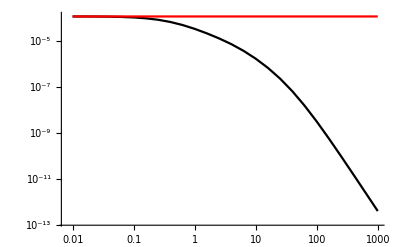

```mathematica
ListLogLogPlot[{Pkt,ptmasstable},Joined->True,PlotStyle->{Black,Red}]
```